```mathematica
Quit[]
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
SetDirectory[NotebookDirectory[]];

enzModelsDir = "/home/mrama/Dropbox/MASSef/examples/"
mainDir=enzModelsDir<>"code_data/";
Import[mainDir<>"sim_plot_functions.m"];
Import[mainDir<>"simulation.m"];
```

/home/mrama/Dropbox/MASSef/examples/

## Simulations

### Systematic simulations

```mathematica
modelList=Import["/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/output/model_simulations/models/model_TPI_all_2.mx"];
```

```mathematica
maxTimeConstants=Table[

jacobian=getJacobian[modelList[[ind]]]/.stripUnits[modelList[[ind]]["InitialConditions"]]/.stripUnits[modelList[[ind]]["Parameters"]];

Max[1/Abs[Re@Eigenvalues[jacobian]]],

{ind,1,Length@modelList}];
```

```mathematica
Sort@maxTimeConstants
```

{3.80679×10^7,5.35279×10^7,9.56463×10^7,1.0342×10^8,1.14396×10^8,2.0165×10^8,3.63418×10^8,4.53961×10^8,5.29427×10^8,1.64095×10^9,2.87775×10^9,4.20659×10^9,4.69279×10^9,8.43283×10^9,9.08276×10^9,1.18968×10^10,1.69838×10^10,2.36647×10^10,2.39809×10^10,2.88813×10^10,2.96373×10^10,3.95224×10^10,5.09132×10^10,5.38747×10^10,8.09327×10^10,9.63607×10^10,9.93584×10^10,1.3027×10^11,2.26223×10^11,2.5458×10^11,2.6761×10^11,2.88674×10^11,3.13911×10^11,3.54993×10^11,3.93598×10^11,4.06904×10^11,4.14513×10^11,4.4661×10^11,7.79222×10^11,8.1593×10^11,1.02108×10^12,1.14919×10^12,1.15408×10^12,1.24743×10^12,1.27505×10^12,1.37731×10^12,2.03749×10^12,2.25992×10^12,2.61984×10^12,2.7134×10^12,2.75144×10^12,3.65062×10^12,6.09292×10^12,6.42168×10^12,8.97424×10^12,9.45696×10^12,9.81906×10^12,1.54121×10^13,1.85818×10^13,3.2257×10^14}

```mathematica
(Times@@Values@FilterRules[modelList[[1]]["Parameters"],{Subscript[k, TPI1]^⟶,Subscript[k, TPI2]^⟶,Subscript[k, TPI3]^⟶}])/
(Times@@Values@FilterRules[modelList[[1]]["Parameters"],{Subscript[k, TPI1]^⟵,Subscript[k, TPI2]^⟵,Subscript[k, TPI3]^⟵}])
```

9.35

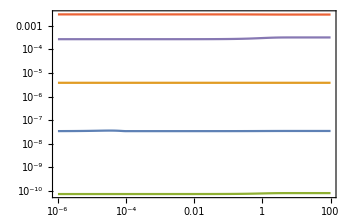

```mathematica
tFinal=100;
{conc,flux}=simulate[modelList[[1]],{t,0,tFinal}];
plotSimulation[conc,{t,0,tFinal}]
```

```mathematica
modelList[[1]]["Species"]
```

{(TPI^c)_^,(TPI^c&dhap^c)_^,dhap^c,g3p^c,(TPI^c&g3p^c)_^}

```mathematica
Values@FilterRules[conc/.t-> tFinal, dhap^c]/Values@FilterRules[conc/.t-> tFinal, g3p^c]
```

{9.35}

```mathematica
conc//Keys
```

{(TPI^c)_^,(TPI^c&dhap^c)_^,(TPI^c&g3p^c)_^,dhap^c,g3p^c}

```mathematica
enzName="TPI";
inputDir = enzModelsDir<>"TPI/fit_TPI/output/model_simulations/models/";
outputDirBase = enzModelsDir<>"TPI/fit_TPI/output/model_simulations/data/";
If[!DirectoryQ[outputDirBase],
	CreateDirectory[outputDirBase,CreateIntermediateDirectories-> True]
];

headerConcMets={"g3p","dhap"};
headerConcEnz={"TPI","TPI&dhap","TPI&g3p"};
headerFlux={"v_TPI1","v_TPI2","v_TPI3"};
subInd = {5};
prodInd={4};
indEnz={1, 2,3};

initCondList={};
outputDirList={"noPerturb"};


tValues=Map[10^#&,Range[-6,2, 0.1]];
tFinal=100;
tValues=Insert[tValues,0., 1];


modelIDList={"all_10000"};
nModelEnsembles={1,1};

 

outputDir =outputDirBase;
If[!DirectoryQ[outputDir<>"/data_mx/"],
	CreateDirectory[outputDir<>"/data_mx/",CreateIntermediateDirectories-> True]
];
```

```mathematica
Do[

simulateEnsembleNoCheck[inputDir, outputDir, enzName, modelID, nModelEnsembles, tFinal, tValues, initCondList, headerConcEnz, headerConcMets, headerFlux, indEnz,subInd, prodInd];,

{modelID, modelIDList}];
```

/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/output/model_simulations/models/model_TPI_all_10000_1.mx